Created by: ruebenko on 05-11-2020 08:02:50

### Categorization

Tutorial

Applications

Applications`

FEMAddOns/tutorial/ThermalLoadOnBeam

Synonyms

FEM

FEA

### Keywords

heat transport

heat transfer

structural mechanics

thermal load

partial differential equation
PDE

Details

# Thermal deformation of elastic beam

Xijun Shi

In this model we calculate displacements in a elastic beam subject to a thermal load. A simple example with the temperature field uniformly changed in the beam is provided for the model verification.

Load the finite element package.

```mathematica
Needs["NDSolve`FEM`"]
```

Set up the system equations.

```mathematica
TransientStructualModel={ρ*Derivative[0, 0, 2][u][x, y, t]+({{0,-(Y ν)/(1-ν^2)},{-(Y (1-ν))/(2 (1-ν^2)),0}}.v[x,y,t]{x,y}Inactive){x,y}Inactive+({{-Y/(1-ν^2),0},{0,-(Y (1-ν))/(2 (1-ν^2))}}.u[x,y,t]{x,y}Inactive){x,y}Inactive,ρ Derivative[0,0,2][v][x,y,t]+({{0,-(Y (1-ν))/(2 (1-ν^2))},{-(Y ν)/(1-ν^2),0}}.u[x,y,t]{x,y}Inactive){x,y}Inactive+({{-(Y (1-ν))/(2 (1-ν^2)),0},{0,-Y/(1-ν^2)}}.v[x,y,t]{x,y}Inactive){x,y}Inactive};
```

Set up material properties for a concrete beam.

```mathematica
Subscript[ρ, c]=2000; (*density in kg/m^3*)
Subscript[Y, c]=20*10^9; (*Young's modulus in Pa*)
Subscript[α, c]=5*10^-6; (*Coefficient of thermal expanison in /C*)
Subscript[ν, c]=0.15; (*Poisson's ratio*)
parameters=
{ρ->Subscript[ρ, c],Y->Subscript[Y, c],ν->Subscript[ν, c],α->Subscript[α, c]};
```

Specify the geometry of the beam.

```mathematica
L=10; (*Length in m*)
H=1; (*Height in m*)
Ω=Rectangle[{0,0},{L,H}];
```

Generate the mesh.

```mathematica
mesh=ToElementMesh[Ω,MaxCellMeasure->5*10^-3];
```

Assuming no temperature gradient in the beam at any time point, and the time of the beam is increasing uniformly)

Set up a temperature field.

```mathematica
Tfun=10t;
```

Temperature increases 10 C/second all over the body in this case. For other applications, Tfun can be any function of time t and position vector {x,y}. Temperature induced loads in x and y directions are then added to the system equations.

Specify the temperature induced loads.

```mathematica
Subscript[F, x]={-(Y α)/(1-ν) Tfun,0}{x,y}Inactive;
```

```mathematica
Subscript[F, y]={0,-(Y α)/(1-ν) Tfun}{x,y}Inactive;
```

Give the initial conditions.

```mathematica
ic={u[x,y,0]==0,v[x,y,0]==0,Derivative[0,0,1][u][x,y,0]==0,Derivative[0,0,1][v][x,y,0]==0};
```

For Boundary conditions we assume the beam is not allowed to expand at the left and bottom surface.

Specify the boundary conditions

```mathematica
Subscript[Γ, fixed]={DirichletCondition[u[x,y,t]==0,x==0],DirichletCondition[v[x,y,t]==0,y==0]};
```

Set up the complete PDE model.

```mathematica
pde ={TransientStructualModel=={Subscript[F, x],Subscript[F, y]},Subscript[Γ, fixed],ic}/.parameters;
```

Solve the model.

```mathematica
measure=AbsoluteTiming[MaxMemoryUsed[Monitor[{ufun,vfun}=NDSolveValue[pde,{u,v},{t,0,30},{x,y}∈mesh,EvaluationMonitor:>(monitor=Row[{"t = ",CForm[t]}])],monitor]]/(1024.^2)];
Print["Time -> ",measure[[1]],"\nMemory -> ", measure[[2]]];
```

Time -> 8.25545
Memory -> 207.034

Visualize the u component of the deformation.

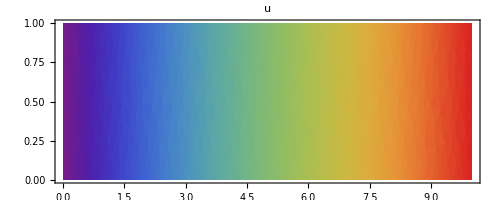

```mathematica
DensityPlot[ufun[x,y,3],{x,y}∈mesh,ColorFunction->"Rainbow",PlotLegends->Placed[Automatic,Bottom],PlotLabel->"u",AspectRatio->Automatic]
```

Visualize the v component of the deformation.

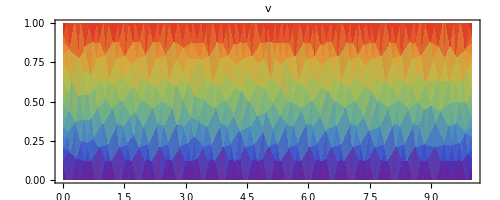

```mathematica
DensityPlot[vfun[x,y,3],{x,y}∈mesh,ColorFunction->"Rainbow",PlotLegends->Placed[Automatic,Bottom],PlotLabel->"v",AspectRatio->Automatic]
```

To verify the result consider that the displacement in the x direction (u) at the right surface should be u=αx(T(t)-T0)xL. At t=3 s, T(t)-T0=30, so that u(t=3)=5 x10^-6 x30x10=0.0015 m.

Verify the result.

```mathematica
ufun[L,H,3]-0.0015
```

-1.3314×10^-16

The result is correct.

More About

Related Tutorials

Related Wolfram Training Courses